```mathematica
ClearAll["Global`*"]
```

```mathematica
logk0=-4;
logkf=1.1;
step=0.01;
bstep=1;
```

```mathematica
ζ[t_]=(1+ⅈ*k*t)*Exp[-ⅈ*k*t];
cζ[t_]:=(1-ⅈ*k*t)*Exp[ⅈ*k*t];
(*η[t_]:=Exp[-(-Log[-t]+5)^2/(1)]*0.05*)
(*η[t_]:=0.05*)
η[t_]:=HeavisideTheta[-Log[-t]+7]*0.05-HeavisideTheta[-Log[-t]+3]*0.05;
```

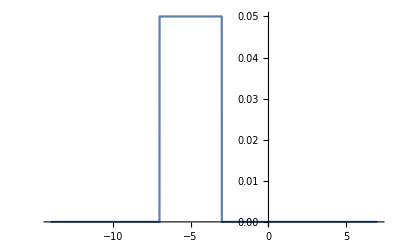

```mathematica
Plot[η[-Exp[-r]],{r,-14, 7},PlotRange->All]
```

```mathematica
list=List[];
list2=List[];
list3=List[];
list4=List[];
Plist=List[];
```

```mathematica
listk:=10^Range[logk0,logkf,step];
"listk:=Range[1, 10 ,1]";
listn0:=N@Subdivide[-14,-3,Length[listk]-1];
"listn0:=N@Subdivide[-5,-5,Length[listk]-1]";
listnf :=N@Subdivide[7,7,Length[listk]-1];
"listnf :=N@Subdivide[15,15,Length[listk]-1]";
```

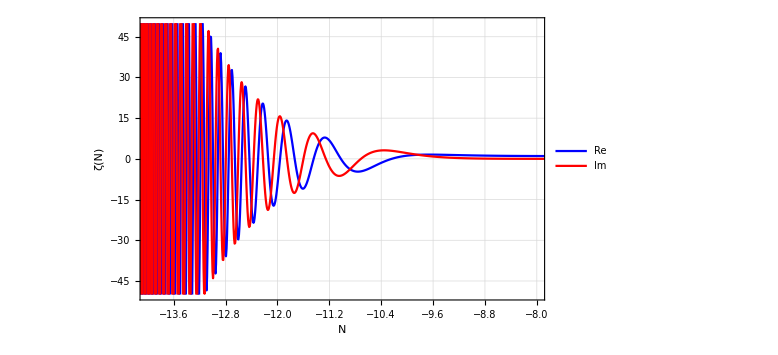

```mathematica
k=listk[[1]];Plot[{Re[ζ[-Exp[-r]]],Im[ζ[-Exp[-r]]] },{r,-20,5},PlotRange->{{-14,-8},{-50,50}},PlotStyle->{Blue,Red}, ImageSize->Large,Frame ->True,FrameLabel->{Style["N", Black, FontSize->24],Style["ζ(N)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, GridLines->Automatic, GridLinesStyle->{{Black, Dotted, Thickness[0.001]}, {Black, Dotted, Thickness[0.001]}}, PlotLegends->Placed[{"Re","Im"}, {0.9,0.8}]]
```

```mathematica
Do[k=listk[[i]];n0=listn0[[i]];nf=listnf[[i]];{s=NDSolve[{
x1'[t]==-ⅈ*η[t]/(k^3*t^3)*(D[cζ[t],t]*ζ[t]*y1[t]+D[cζ[t],t]*cζ[t]*y2[t]), 
x2'[t]==-ⅈ*η[t]/(k^3*t^3)*(-D[ζ[t],t]*ζ[t]*y1[t]+-D[ζ[t],t]*cζ[t]*y2[t]),
y1'[t]==ⅈ*η[t]/(k^3*t^3)*(-D[ζ[t],t]*cζ[t]*x1[t]+-D[cζ[t],t]*cζ[t]*x2[t]),
y2'[t]==ⅈ*η[t]/(k^3*t^3)*(D[ζ[t],t]*ζ[t]*x1[t]+D[cζ[t],t]*ζ[t]*x2[t]),
x1[-Exp[-n0]]==1, x2[-Exp[-n0]]==0, y1[-Exp[-n0]]==0, y2[-Exp[-n0]]==0},{x1,x2,y1,y2},{t,-Exp[-n0],-Exp[-nf]}],
 xx2[t_]:=x2[t]/.s, points1=Table[{k,n,xx2[-Exp[-n]]},{n,nf,nf,step}], nk=points1[[-1]],AppendTo[list,{nk[[1]],nk[[3]][[1]]}],
 xx1[t_]:=x1[t]/.s, points2=Table[{k,n,xx1[-Exp[-n]]},{n,nf,nf,step}], nk2=points2[[-1]],AppendTo[list2,{nk2[[1]],nk2[[3]][[1]]}] },
{i, 1, Length[listk], 1}]
```

```mathematica
Do[k=listk[[i]];n0=listn0[[i]];nf=listnf[[i]];{s2=NDSolve[{
x1'[t]==-ⅈ*η[t]/(k^3*t^3)*(D[cζ[t],t]*ζ[t]*y1[t]+D[cζ[t],t]*cζ[t]*y2[t]), x2'[t]==-ⅈ*η[t]/(k^3*t^3)*(-D[ζ[t],t]*ζ[t]*y1[t]+-D[ζ[t],t]*cζ[t]*y2[t]),y1'[t]==ⅈ*η[t]/(k^3*t^3)*(-D[ζ[t],t]*cζ[t]*x1[t]+-D[cζ[t],t]*cζ[t]*x2[t]),
y2'[t]==ⅈ*η[t]/(k^3*t^3)*(D[ζ[t],t]*ζ[t]*x1[t]+D[cζ[t],t]*ζ[t]*x2[t]), 
x1[-Exp[-n0]]==0, x2[-Exp[-n0]]==0, y1[-Exp[-n0]]==1, y2[-Exp[-n0]]==0},{x1,x2,y1,y2},{t,-Exp[-n0],-Exp[-nf]}], xx22[t_]:=x2[t]/.s2, points3=Table[{k,n,xx22[-Exp[-n]]},{n,nf,nf,step}], nk3=points3[[-1]],AppendTo[list3,{nk3[[1]],nk3[[3]][[1]]}], xx11[t_]:=x1[t]/.s2, points4=Table[{k,n,xx11[-Exp[-n]]},{n,nf,nf,step}], nk4=points4[[-1]],AppendTo[list4,{nk4[[1]],nk4[[3]][[1]]}] }, {i, 1, Length[listk], 1}]
```

```mathematica
Do[AppendTo[Plist,List[list[[i]][[1]],(Abs[list[[i]][[2]]+list2[[i]][[2]]])^2+(Abs[list3[[i]][[2]]+ list4[[i]][[2]]])^2]],{i,1,Length[listk],1}]
Plist;
```

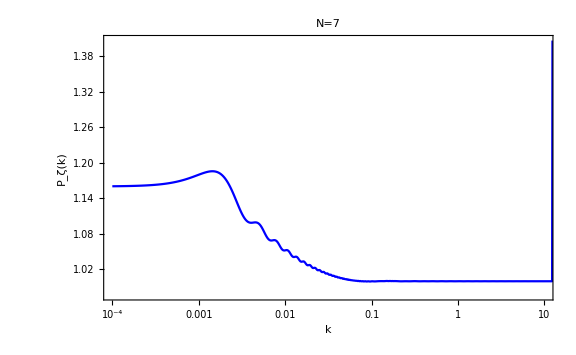

```mathematica
ListLogLinearPlot[{Plist}, PlotStyle->Blue, ImageSize->Large,Frame ->True,FrameLabel->{Style["k", Black, FontSize->24],Style["P_ζ(k)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, GridLines->Automatic, GridLinesStyle->{{Black, Dotted, Thickness[0.001]}, {Black, Dotted, Thickness[0.001]}}, PlotLabel->Style["N="<>ToString[IntegerPart[listnf[[1]]]], Black, FontSize->20], PlotRange->{{10^-4,10},Automatic}, Joined->True]
```

```mathematica
listalpha1R := List[];
listalpha1I := List[];
listbeta1R := List[];
listbeta1I := List[];
listalpha2R := List[];
listalpha2I := List[];
listbeta2R := List[];
listbeta2I := List[];
Do[AppendTo[listalpha1R,List[list2[[i]][[1]],Re[list2[[i]][[2]]]]],{i,1,Length[listk],1}];
Do[AppendTo[listalpha1I,List[list2[[i]][[1]],Im[list2[[i]][[2]]]]],{i,1,Length[listk],1}];
Do[AppendTo[listbeta1R,List[list[[i]][[1]],Re[list[[i]][[2]]]]],{i,1,Length[listk],1}];
Do[AppendTo[listbeta1I,List[list[[i]][[1]],Im[list[[i]][[2]]]]],{i,1,Length[listk],1}];
Do[AppendTo[listalpha2R,List[list4[[i]][[1]],Re[list4[[i]][[2]]]]],{i,1,Length[listk],1}];
Do[AppendTo[listalpha2I,List[list4[[i]][[1]],Im[list4[[i]][[2]]]]],{i,1,Length[listk],1}];
Do[AppendTo[listbeta2R,List[list3[[i]][[1]],Re[list3[[i]][[2]]]]],{i,1,Length[listk],1}];
Do[AppendTo[listbeta2I,List[list3[[i]][[1]],Im[list3[[i]][[2]]]]],{i,1,Length[listk],1}];
```

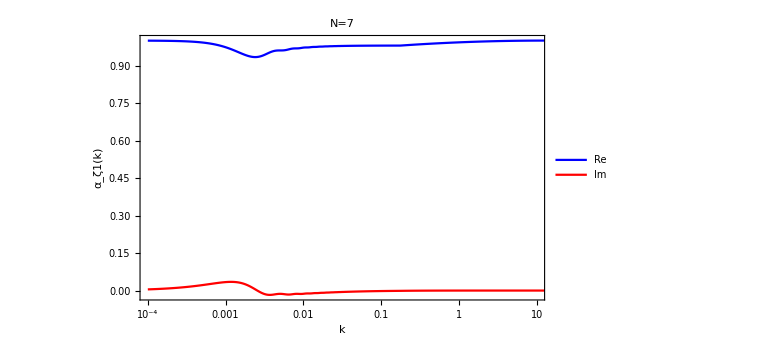

```mathematica
p1=ListLogLinearPlot[{listalpha1R,listalpha1I}, PlotStyle->{Blue,Red}, ImageSize->Large,Frame ->True,FrameLabel->{Style["k", Black, FontSize->24],Style["α_ζ1(k)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, GridLines->Automatic, GridLinesStyle->{{Black, Dotted, Thickness[0.001]}, {Black, Dotted, Thickness[0.001]}}, PlotLabel->Style["N="<>ToString[IntegerPart[listnf[[1]]]], Black, FontSize->20], PlotRange->{{10^-4,10},Automatic}, Joined->True,PlotLegends->Placed[{"Re","Im"}, {0.9,0.67}]]
```

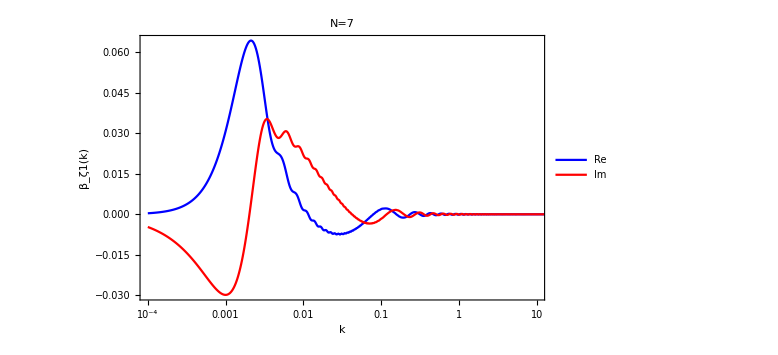

```mathematica
p2=ListLogLinearPlot[{listbeta1R,listbeta1I}, PlotStyle->{Blue,Red}, ImageSize->Large,Frame ->True,FrameLabel->{Style["k", Black, FontSize->24],Style["β_ζ1(k)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, GridLines->Automatic, GridLinesStyle->{{Black, Dotted, Thickness[0.001]}, {Black, Dotted, Thickness[0.001]}}, PlotLabel->Style["N="<>ToString[IntegerPart[listnf[[1]]]], Black, FontSize->20], PlotRange->{{10^-4,10},Full}, Joined->True,PlotLegends->Placed[{"Re","Im"}, {0.9,0.8}]]
```

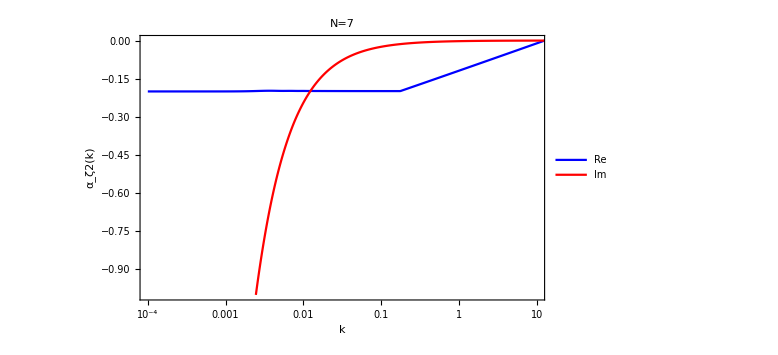

```mathematica
p3=ListLogLinearPlot[{listalpha2R,listalpha2I}, PlotStyle->{Blue,Red}, ImageSize->Large,Frame ->True,FrameLabel->{Style["k", Black, FontSize->24],Style["α_ζ2(k)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, GridLines->Automatic, GridLinesStyle->{{Black, Dotted, Thickness[0.001]}, {Black, Dotted, Thickness[0.001]}}, PlotLabel->Style["N="<>ToString[IntegerPart[listnf[[1]]]], Black, FontSize->20], PlotRange->{{10^-4,10},Automatic}, Joined->True,PlotLegends->Placed[{"Re","Im"}, {0.9,0.67}]]
```

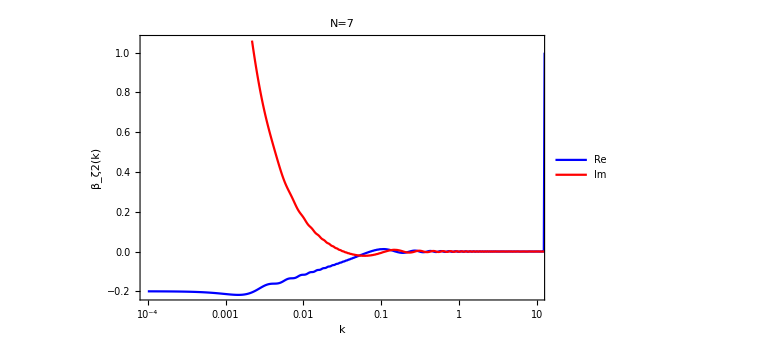

```mathematica
p4=ListLogLinearPlot[{listbeta2R,listbeta2I}, PlotStyle->{Blue,Red}, ImageSize->Large,Frame ->True,FrameLabel->{Style["k", Black, FontSize->24],Style["β_ζ2(k)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, GridLines->Automatic, GridLinesStyle->{{Black, Dotted, Thickness[0.001]}, {Black, Dotted, Thickness[0.001]}}, PlotLabel->Style["N="<>ToString[IntegerPart[listnf[[1]]]], Black, FontSize->20], PlotRange->{{10^-4,10},Automatic}, Joined->True,PlotLegends->Placed[{"Re","Im"}, {0.9,0.8}]]
```

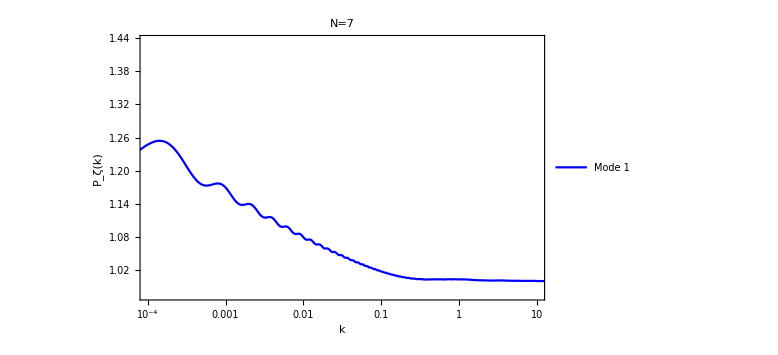

```mathematica
p4=ListLogLinearPlot[{(Abs[listbeta1R+listbeta1I + listalpha1R+listalpha1I])^2+ (Abs[listbeta2R+listbeta2I + listalpha2R+listalpha2I])^2}, PlotStyle->{Blue,Red}, ImageSize->Large,Frame ->True,FrameLabel->{Style["k", Black, FontSize->24],Style["P_ζ(k)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, GridLines->Automatic, GridLinesStyle->{{Black, Dotted, Thickness[0.001]}, {Black, Dotted, Thickness[0.001]}}, PlotLabel->Style["N="<>ToString[IntegerPart[listnf[[1]]]], Black, FontSize->20], PlotRange->{{10^-4,10},Automatic}, Joined->True,PlotLegends->Placed[{"Mode 1","Mode 2"}, {0.9,0.8}]]
```

```mathematica
Plist1:=List[]
Plist2:=List[]
```

```mathematica
Do[AppendTo[Plist1,List[list[[i]][[1]],(Abs[list[[i]][[2]]+list2[[i]][[2]]])^2]],{i,1,Length[listk],1}]
Do[AppendTo[Plist2,List[list[[i]][[1]],(Abs[list3[[i]][[2]]+ list4[[i]][[2]]])^2]],{i,1,Length[listk],1}]
```

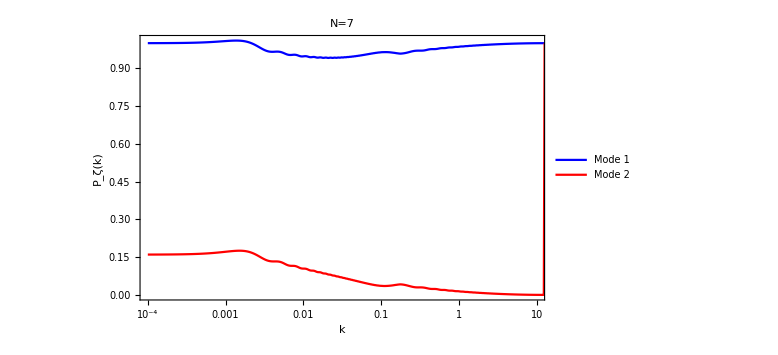

```mathematica
ListLogLinearPlot[{Plist1,Plist2}, PlotStyle->{Blue,Red}, ImageSize->Large,Frame ->True,FrameLabel->{Style["k", Black, FontSize->24],Style["P_ζ(k)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, GridLines->Automatic, GridLinesStyle->{{Black, Dotted, Thickness[0.001]}, {Black, Dotted, Thickness[0.001]}}, PlotLabel->Style["N="<>ToString[IntegerPart[listnf[[1]]]], Black, FontSize->20], PlotRange->{{10^-4,10},Automatic}, Joined->True,PlotLegends->Placed[{"Mode 1","Mode 2"}, {0.9,0.8}]]
```

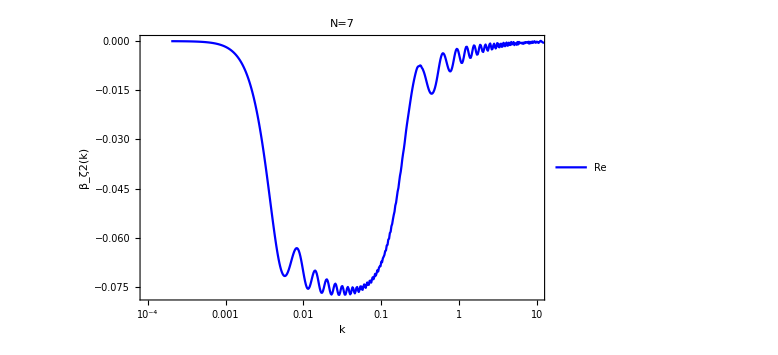

```mathematica
p4=ListLogLinearPlot[{listalpha2I+listbeta2I}, PlotStyle->{Blue,Red}, ImageSize->Large,Frame ->True,FrameLabel->{Style["k", Black, FontSize->24],Style["β_ζ2(k)", Black, FontSize->24]},FrameTicksStyle->Directive["Label", 18, Black], LabelStyle->{FontSize->16}, GridLines->Automatic, GridLinesStyle->{{Black, Dotted, Thickness[0.001]}, {Black, Dotted, Thickness[0.001]}}, PlotLabel->Style["N="<>ToString[IntegerPart[listnf[[1]]]], Black, FontSize->20], PlotRange->{{10^-4,10},Automatic}, Joined->True,PlotLegends->Placed[{"Re","Im"}, {0.9,0.8}]]
```